```mathematica
DD2[n_,k_]:=DD2[n,k]=Sum[ DD2[Floor[n/j],k-1],{j,2,n}];DD2[n_,0]:=1
DDD[n_,z_]:=Sum[FactorialPower[z,a]/a! DD2[n,a],{a,0,Log[2,n]}]
K[n_]:=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
P[n_, k_]:=Sum[ K[j] P[Floor[n/j],k-1],{j,2,n}];P[n_,0]:=1
```

```mathematica
da[n_,z_]:=Product[Pochhammer[z,a=p[[2]]]/a!,{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
daa[z_] := da[8,z]
Expand[daa'[z]]
```

1/3+z+z^2/2

```mathematica
Table[ P[100,k]/(k-1)!,{k,1,7}]
```

{428/15,16289/180,993/16,611/36,67/48,7/120,0}

```mathematica
faa[z_] := DDDa[100,z]
faa'[z]
Expand[FullSimplify[faa'[z]]]
```

DDDa^(0,1)[100,z]

DDDa^(0,1)[100,z]

```mathematica
d2d[ n_, z_]:=Sum[ 1/(k!) DD2[n,k] FactorialPower[z,k] (-PolyGamma[0,(-k+1)+z]+PolyGamma[0,1+z]),{k,1,Log[2,n]}]
d2e[ n_, z_]:=Sum[ 1/(k!) DD2a[n,k] FactorialPower[z,k](-PolyGamma[0,(-k+1)+z]+PolyGamma[0,1+z]),{k,1,Log[2,n]}]
```

```mathematica
d2e[100,2]
```

Infinity::indet: Indeterminate expression 0\ DD2a[100, 3]\ ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0\ DD2a[100, 4]\ ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0\ DD2a[100, 5]\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Indeterminate

```mathematica
fa[z_] := DDD[100,z]
Expand[FullSimplify[fa'[z]]]
```

428/15+(16289 z)/180+(993 z^2)/16+(611 z^3)/36+(67 z^4)/48+(7 z^5)/120

```mathematica
D[DDD[100,z],z]
```

99+7/720 FactorialPower[z,6] (-PolyGamma[0,-5+z]+PolyGamma[0,1+z])+17/40 FactorialPower[z,5] (-PolyGamma[0,-4+z]+PolyGamma[0,1+z])+23/3 FactorialPower[z,4] (-PolyGamma[0,-3+z]+PolyGamma[0,1+z])+54 FactorialPower[z,3] (-PolyGamma[0,-2+z]+PolyGamma[0,1+z])+283/2 FactorialPower[z,2] (-PolyGamma[0,-1+z]+PolyGamma[0,1+z])

```mathematica
FullSimplify[D[DDD[100,z],z]]/.z->0
```

428/15

```mathematica
Expand[FullSimplify[fa[z]]]
```

1+99 z+283/2 FactorialPower[z,2]+54 FactorialPower[z,3]+23/3 FactorialPower[z,4]+17/40 FactorialPower[z,5]+7/720 FactorialPower[z,6]

```mathematica
Expand[FullSimplify[fa[b]]]
```

1+99 b+283/2 FactorialPower[b,2]+54 FactorialPower[b,3]+23/3 FactorialPower[b,4]+17/40 FactorialPower[b,5]+7/720 FactorialPower[b,6]

```mathematica
fc[z_] := 428/15+(16289 z)/180+(993 z^2)/16+(611 z^3)/36+(67 z^4)/48+(7 z^5)/120
```

```mathematica
1+Integrate[ fc[z],{z,0,-3}]
```

47

```mathematica
DDD[100,-3]
```

47

```mathematica
fc[0]
```

428/15

```mathematica
1+Integrate[ fc[z],{z,0,3}]
```

1471

```mathematica
DDD[100,3]
```

1471

```mathematica
1+Integrate[ fc[z],{z,0,1-3I}]
```

-5279/8+(3335 ⅈ)/8

```mathematica
DDD[100,1-3I]
```

-5279/8+(3335 ⅈ)/8

```mathematica
Integrate[ fc[z],{z,1,2}]
```

382

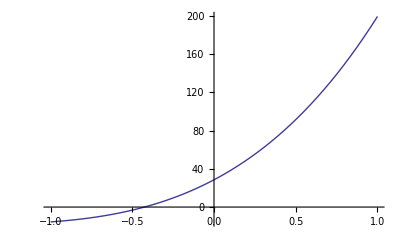

```mathematica
Plot[ {fc[z]},{z,-1,1}]
```

```mathematica
c1:=CoefficientList[Series[Log[1+x],{x,0,20}],x]
c2:=CoefficientList[Series[Log[1+x]^2,{x,0,20}],x]
c3:=CoefficientList[Series[Log[1+x]^3,{x,0,20}],x]
c4:=CoefficientList[Series[Log[1+x]^4,{x,0,20}],x]
c5:=CoefficientList[Series[Log[1+x]^5,{x,0,20}],x]
c6:=CoefficientList[Series[Log[1+x]^6,{x,0,20}],x]
c7:=CoefficientList[Series[Log[1+x]^7,{x,0,20}],x]
ca := { c1, c2, c3, c4, c5, c6, c7}
```

```mathematica
428/15+(16289 z)/180+(993 z^2)/16+(611 z^3)/36+(67 z^4)/48+(7 z^5)/120
```

```mathematica
Sum[ ca[[1]][[k+1]]DD2[100, k],{k,1,7}]
```

428/15

```mathematica
Sum[ Sum[ ca[[j]][[k+1]]DD2[100, k]/((j-1)!)z^(j-1),{k,1,7}], {j,1,7}]
```

428/15+(16289 z)/180+(993 z^2)/16+(611 z^3)/36+(67 z^4)/48+(7 z^5)/120

```mathematica
Sum[ DD2a[100, k] Sum[ ca[[j]][[k+1]]/((j-1)!)z^(j-1), {j,1,7}],{k,1,7}]
```

DD2a[100,1]+(-1/2+z) DD2a[100,2]+(1/3-z+z^2/2) DD2a[100,3]+(-1/4+(11 z)/12-(3 z^2)/4+z^3/6) DD2a[100,4]+(1/5-(5 z)/6+(7 z^2)/8-z^3/3+z^4/24) DD2a[100,5]+(-1/6+(137 z)/180-(15 z^2)/16+(17 z^3)/36-(5 z^4)/48+z^5/120) DD2a[100,6]+(1/7-(7 z)/10+(29 z^2)/30-(7 z^3)/12+(25 z^4)/144-z^5/40+z^6/720) DD2a[100,7]

```mathematica
dif[k_] := (DDD[ 100, k ] - DDD[ 100, -k ])/(2k)
```

```mathematica
dif[.0001]
```

28.5333

```mathematica
D2[n_,k_,s_]:=Sum[j^-s D2[Floor[n/j],k-1,s],{j,2,n}];D2[n_,0,s_]:=1
DD[n_,z_,s_]:=Sum[FactorialPower[z,a]/a! D2[n,a,s],{a,0,Log[2,n]}]
dif[k_,s_] := (DD[ 100, k,s ] - DD[ 100, -k,s ])/(2k)
```

```mathematica
N[dif[.0001,-1]]
```

1156.48

```mathematica
(DD[100, .0001, -1]-1)/.0001
```

1156.72

```mathematica
fs[s_] := x^s
```

```mathematica
fs'[s]
```

x^s Log[x]

```mathematica
fo[s_] := (1-Gamma[s,-Log[100]]/Gamma[s])
```

```mathematica
Limit[fo'[s],s->0]
```

Limit[-(Gamma[s,-Log[100]] (ⅈ π+Log[Log[100]])+MeijerG[{{},{1,1}},{{0,0,s},{}},-Log[100]])/Gamma[s]+(Gamma[s,-Log[100]] PolyGamma[0,s])/Gamma[s],s→0]

```mathematica
D2[n_,k_,s_]:=D2[n,k,s]=Sum[j^-s D2[Floor[n/j],k-1,s],{j,2,n}];D2[n_,0,s_]:=1
DD[n_,z_,s_]:=Sum[FactorialPower[z,a]/a! D2[n,a,s],{a,0,Log[2,n]}]
```

```mathematica
g1[s_] := DD[10,z,s]
g1a[s_] := DD[100,z,s]
```

```mathematica
g1[0]
```

1+99 z+283/2 FactorialPower[z,2]+54 FactorialPower[z,3]+23/3 FactorialPower[z,4]+17/40 FactorialPower[z,5]+7/720 FactorialPower[z,6]

```mathematica
Integrate[ g1a'[s],{s,0,Infinity}]
```

$Aborted

```mathematica
gg[zz_,s_] :=g1'[s]/.z->zz
gga[zz_,s_] :=g1a'[s]/.z->zz
```

```mathematica
g2[s_] := D2[10,1,s]
```

```mathematica
Expand[g2'[s]]
```

-2^-s Log[2]-3^-s Log[3]-4^-s Log[4]-5^-s Log[5]-6^-s Log[6]-7^-s Log[7]-8^-s Log[8]-9^-s Log[9]-10^-s Log[10]

```mathematica
Integrate[ gg[1,s],{s,0,-1}]
```

45

```mathematica
DD[10,2,0]+Integrate[ gg[2,s],{s,0,-1}]
```

170

```mathematica
DD[10,2,-1]
```

170

```mathematica
DD[10,3,0]+Integrate[ gg[3,s],{s,0,-2}]
```

2708

```mathematica
DD[10,3,-2]
```

2708

```mathematica
DD[10,3,3]+Integrate[ gg[3,s],{s,3,-2}]
```

2708

```mathematica
1-Integrate[ gg[3,s],{s,-2,Infinity}]
```

2708

```mathematica
(DD[10,.00000001,0]+Integrate[ gg[.00000001,s],{s,0,-2}]-1)/.00000001
```

156.833

```mathematica
(DD[10,.00000001,-2]-1)/.00000001
```

156.833

```mathematica
(-Integrate[ gg[.00000001,s],{s,-2,Infinity}])/.00000001
```

156.833

```mathematica
(DD[10,.0000001,-2]-Integrate[ gg[.0000001,s],{s,0,-2}]-1)/.0000001
```

5.33333

```mathematica
(-Integrate[ gg[.00000001,s],{s,0,Infinity}])/.00000001
```

5.33333

```mathematica
(DD[10,.0000001,0]-1)/.0000001
```

5.33333

```mathematica
DD[10,.0000001,-2]
```

1.00002

```mathematica
Integrate[ gg[.0000001,s],{s,0,-2}]
```

0.00001515

```mathematica
(-Integrate[ gga[.00000001,s],{s,0,Infinity}])/.00000001
```

$Aborted

```mathematica
(Integrate[- gg[.00000001,s]/.00000001,{s,0,Infinity}])
```

5.33333

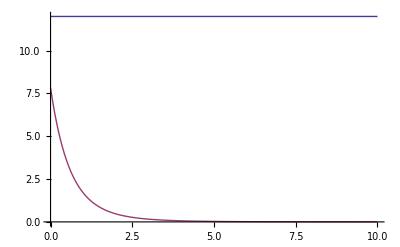

```mathematica
Plot[{12,-gg[.000000001,s]/.000000001},{s,0,10}]
```

```mathematica
-gga[.0000000001,0]/.0000000001
```

94.0453

```mathematica
N[Sum[ MangoldtLambda[ j],{j,2,100}]]
```

94.0453

```mathematica
N[Limit[-gga[s,0]/s,{s->0}]]
```

{94.0453}

```mathematica
-gga[1.,0]
```

363.739

```mathematica
Plot[{12,-gg[.000001,s]/.000001},{s,0,10}]
```

-Graphics-

```mathematica
Limit[-gg[k,s]/k,{k->0}]
```

{4^-s (-1+2^s) Log[2]+9^-s (-1+3^s) Log[3]+2^(-1-3 s) Log[4]+4^-s Log[4]+5^-s Log[5]+7^-s Log[7]+9^-s Log[9]}

```mathematica
ga[s_] := 4^-s (-1+2^s) Log[2]+9^-s (-1+3^s) Log[3]+2^(-1-3 s) Log[4]+4^-s Log[4]+5^-s Log[5]+7^-s Log[7]+9^-s Log[9]
```

```mathematica
Integrate[ ga[s],{s,0,Infinity}]
```

16/3

```mathematica
Integrate[ ga[s],{s,0, I Infinity}]
```

∫_0^(ⅈ ∞) (4^-s (-1+2^s) Log[2]+9^-s (-1+3^s) Log[3]+2^(-1-3 s) Log[4]+4^-s Log[4]+5^-s Log[5]+7^-s Log[7]+9^-s Log[9])ⅆs

```mathematica
Sum[Log[2]/2^s,{s,0,Infinity}]
```

2 Log[2]

```mathematica
Integrate[Log[2]/2^s,{s,0,Infinity}]
```

1

```mathematica
Integrate[ ga[s],{s,0,1}]
```

2479/630

```mathematica
(DD[10,.0000001,1]-1)/.0000001
```

1.39841

```mathematica
D[x^n, x]
```

n x^(-1+n)

```mathematica
D[x^n, n]
```

x^n Log[x]

```mathematica
D[DD[10,z,s],s]
```

-2^(-1-3 s) FactorialPower[z,3] Log[2]+1/2 FactorialPower[z,2] (-2^-s (2^-s+3^-s+4^-s+5^-s) Log[2]-3^-s (2^-s+3^-s) Log[3]+3^-s (-2^-s Log[2]-3^-s Log[3])+2^-s (-2^-s Log[2]-3^-s Log[3]-4^-s Log[4]-5^-s Log[5])-8^-s Log[8]-10^-s Log[10])+z (-2^-s Log[2]-3^-s Log[3]-4^-s Log[4]-5^-s Log[5]-6^-s Log[6]-7^-s Log[7]-8^-s Log[8]-9^-s Log[9]-10^-s Log[10])

```mathematica
Integrate[-D[ DD[10,.00000001,s],s]/.00000001,{s,0,Infinity}]
```

5.33333

```mathematica
1-Integrate[D[ DD[10,2,s],s],{s,-1,Infinity}]
```

170

```mathematica
DD[10,2,-1]
```

170

```mathematica
Limit[ -z^-1 Integrate[D[ DD[10,z,s],s],{s,0,Infinity}],{z->0}]
```

{16/3}

```mathematica
Limit[( DD[10,z,0]-1)/z,{z->0}]
```

{16/3}

```mathematica
FullSimplify[Limit[ Integrate[-D[ DD[10,z,s],s]/z,{s,-1,Infinity}],{z->0}]]
```

{157/6}

```mathematica
FullSimplify[Limit[ Integrate[-D[ DD[10,z,s],s]/z,{s,1,Infinity}],{z->0}]]
```

{881/630}

```mathematica
Limit[( DD[10,z,1]-1)/z,{z->0}]
```

{881/630}

```mathematica
1+1
```

```mathematica
-gga[.0000000001,0]/.0000000001
```

94.0453

```mathematica
L2[n_, k_ ]:= Sum[ L2[Floor[n/j],k-1],{j,2,n}];L2[n_, 1] := Sum[ Log[j],{j,2,n}]
L2toL1x[n_,z_]:=Sum[Binomial[z-1,a] L2[n,a+1],{a,0,Log[2,n]}]
```

```mathematica
N[Limit[ D[ (-DD[100,z,s]-1)/z,s]/.s->0, z->0]]
```

94.0453

```mathematica
Limit[ ( DD[100,z,0]-1)/z, z->0]
```

428/15

```mathematica
FullSimplify[D[DD[100,z,0],z]]/.z->0
```

428/15

```mathematica
N[D[-DD[100,-.5I,s]/-.5I,s]/.s->0]
```

-73.7152+82.3658 ⅈ

```mathematica
N[L2toL1x[100,-.5I]]
```

73.7152-82.3658 ⅈ

```mathematica
N[D[-DD[100,1,s]/1,s]/.s->0]
```

363.739

```mathematica
N[L2toL1x[100,1]]
```

363.739

```mathematica
N[L2toL1x[100,2]]
```

920.841

```mathematica
N[D[-DD[100,2,s]/2,s]/.s->0]
```

920.841

```mathematica
FullSimplify[D[DD[100,z,0],z]]/.z->0
```

428/15

```mathematica
N[Integrate[ D[-DD[100,k,s]/k,s]/.s->0,{k,0,1}]]
```

210.494

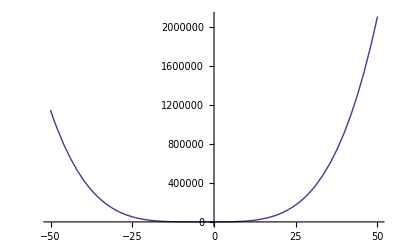

```mathematica
Plot[D[DD[50,z,0],z]/.z->z2,{z2,-50,50}]
```

```mathematica
D[DD[50,z,0],z]
```

```mathematica
ss[z_]:=49+1/20 FactorialPower[z,5] (-PolyGamma[0,-4+z]+PolyGamma[0,1+z])+35/24 FactorialPower[z,4] (-PolyGamma[0,-3+z]+PolyGamma[0,1+z])+46/3 FactorialPower[z,3] (-PolyGamma[0,-2+z]+PolyGamma[0,1+z])+54 FactorialPower[z,2] (-PolyGamma[0,-1+z]+PolyGamma[0,1+z])
```

```mathematica
Expand[FullSimplify[D[DD[100,z,0],z]]]
```

428/15+(16289 z)/180+(993 z^2)/16+(611 z^3)/36+(67 z^4)/48+(7 z^5)/120

```mathematica
Integrate[ -D[DO[n,z,t]/z,z],{t,b,c}]
```

∫_b^c (DO[n,z,t]/z^2-(DO^(0,1,0)[n,z,t])/z)ⅆt

```mathematica
D2[n_,k_,s_]:=D2[n,k,s]=Sum[j^-s D2[Floor[n/j],k-1,s],{j,2,n}];D2[n_,0,s_]:=1
DD[n_,z_,s_]:=Sum[FactorialPower[z,a]/a! D2[n,a,s],{a,0,Log[2,n]}]
```

```mathematica
N[Limit[ D[ (-DD[100,z,s]-1)/z,s]/.s->0, z->0]]
```

94.0453

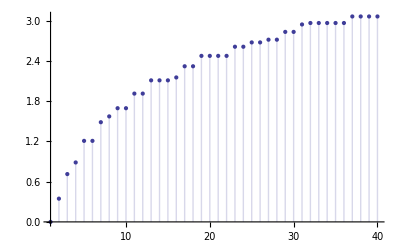

```mathematica
DiscretePlot[ Limit[ D[ (-DD[n,z,s]-1)/z,s]/.s->1, z->0],{n,1,40}]
```

```mathematica
FullSimplify[Limit[ D[ (-DD[30,z,s]-1)/z,s], z->0]-Limit[ D[ (-DD[29,z,s]-1)/z,s], z->0]]
```

0

```mathematica
FullSimplify[Limit[ D[ (-DD[31,z,s]-1)/z,s], z->0]-Limit[ D[ (-DD[30,z,s]-1)/z,s], z->0]]
```

31^-s Log[31]

```mathematica
31 31 31
```

29791

```mathematica
FullSimplify[Sum[ MangoldtLambda[ j ]/Log[j] Integrate[ Log[j] j^-s,{s,0,Infinity}],{j,2,100}]]
```

428/15

```mathematica
FullSimplify[Limit[ D[ (-DD[31,z,s]-1)/z,s], z->1]-Limit[ D[ (-DD[30,z,s]-1)/z,s], z->1]]
```

31^-s Log[31]

```mathematica
Table[ FullSimplify[D[DD[100,z,0],{z,s}]]/.z->0,{s,0,4}]
```

{1,428/15,16289/180,993/8,611/6}

```mathematica
Table[ P[100,k],{k,0,7}]
```

{1,428/15,16289/180,993/8,611/6,67/2,7,0}

```mathematica
Table[Limit[FullSimplify[D[(DD[100,z,0]-1)/z,{z,s}]],z->0],{s,0,3}]
```

{428/15,16289/360,331/8,611/24}

```mathematica
Table[ P[100,k]/k,{k,1,7}]
```

{428/15,16289/360,331/8,611/24,67/10,7/6,0}

```mathematica
N[Limit[ D[ (DD[100,z,s]-1)/z,{s,0}]/.s->0, z->0]]
```

28.5333

```mathematica
N[Sum[ Log[j]^0 K[j],{j,2,100}]]
```

28.5333

```mathematica
N[Limit[ D[ (DD[100,z,s]-1)/z,{s,1}]/.s->0, z->0]]
```

-94.0453

```mathematica
N[Sum[ (-1)^(1)Log[j] K[j],{j,2,100}]]
```

-94.0453

```mathematica
N[Limit[ D[ (DD[100,z,s]-1)/z,{s,2}]/.s->0, z->0]]
```

342.318

```mathematica
N[Sum[(-1)^(2) Log[j]^2 K[j],{j,2,100}]]
```

342.318

```mathematica
N[Limit[ D[ (DD[100,z,s]-1)/z,{s,3}]/.s->0, z->0]]
```

-1311.28

```mathematica
N[Sum[ (-1)^(3)Log[j]^3 K[j],{j,2,100}]]
```

-1311.28

```mathematica
N[Limit[ D[ (DD[100,z,s]-1)/z,{s,4}]/.s->0, z->0]]
```

5178.95

```mathematica
N[Sum[ (-1)^4 Log[j]^4 K[j],{j,2,100}]]
```

5178.95

```mathematica
N[Limit[ D[ (DD[100,z,s]),{z,1}]/.s->0, z->0]]
```

28.5333

```mathematica
tt[n_, k_] := Sum[ (-1)^(k)Log[j]^k K[j]/k!,{j,2,100}]
```

```mathematica
lx[n_, x_] := tt[n,0]+Sum[ tt[n,j] x^j,{j,1,30}]
```

```mathematica
N[lx[100,-1]]
```

1156.48

```mathematica
N[Limit[ (DD[100,z,-1]-1)/z,z->0]]
```

1156.48